Nhi Nguyen
UCI ID: 76164237
Math 9 Final Exam

Problem 4

```mathematica
f[x_]:=2+(1/x)
```

Part a

```mathematica
g[x_]:=Piecewise[{{f[x],x≥1},{3*x,x<1}}]
```

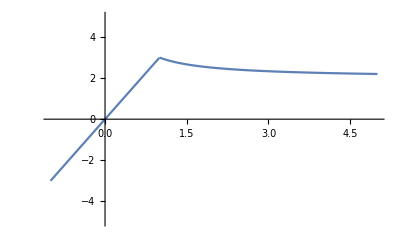

```mathematica
Plot[g[x],{x,-1,5},PlotRange->{{-1,5},{-5,5}}]
```

Part b

```mathematica
n=Nest[f[#]&,2,10];
```

```mathematica
N[(Sqrt[2]+1)-n]
```

1.0727×10^-8